```mathematica
axiom=InputString["Введите аксиому"];
newF=InputString["Введите порождающее правило newF"];
newb=InputString["Введите порождающее правило newb"];
level=Input["Введите число итераций"];
W=axiom;
For[i=1,i≤level,T="";
For[j=1,j≤StringLength[W],l=StringTake[W,{j}];
If[l=="+",T=T<>"+"];
If[l=="-",T=T<>"-"];
If[l=="F",T=T<>newF];
If[l=="[",T=T<>"["];
If[l=="]",T=T<>"["];
If[l=="b",T=T<>"b"];
j++];
W=T;i++];
W
```

FF-[F]+[F]FF-[F]+[F]-[FF-[F]+[F][+[FF-[F]+[F][

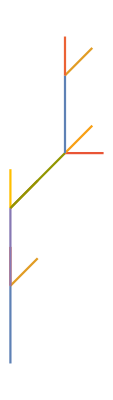

```mathematica
T={0,0};
stack={};
alpha=Input["Введите начальное направление движения"];
theta=Input["Введите величину приращения по углу тета"];
For[j=1;i=1;path[i]={T},j≤StringLength[W],l=StringTake[W,{j}];
If[l=="+",alpha=alpha+theta];
If[l=="-",alpha=alpha-theta];
If[l=="F",T=T+{Cos[alpha],Sin[alpha]};
path[i]=path[i]~Join~{T}];
If[l=="b",i++;T=T+{Cos[alpha],Sin[alpha]};path[i]={T}];
If[l=="[",i++;stack=stack~Join~{Append[T,alpha]};
path[i]={T}];
If[l=="]",i++;T=T=stack[[-1,1;;2]];alpha=stack[[-1,3]];
stack=stack[[1;;-2]];path[i]={T}];j++]
Print[ListLinePlot[Table[path[k],{k,i}],Axes->False,PlotRange->All,AspectRatio->Automatic]]
```